# IoT Connectivity and the Wolfram Blockchain

by Tony Koop
Mentor - Matthew Szudzik
with special help from Jesse Friedman

The World Meteorological Organization has over 11,000 weather stations around the world. The data from these devices are continuously recorded into public databases and made available for anyone to download and analyze. Meteorologists regularly inform their viewers with reports produced by Weather, Research & Forecast (WRF) models which analyze these aggregated datasets. In addition to the WMO’s stations, there are also civilian owned weather stations that inform platforms like Weather Underground, AcuRite, and Weather Bug. Unfortunately, those companies do not share the profits they generate off the data they collect from the community and some companies, like AcuRite, no longer offer a public API for their users to easily access their own data. Even worse, WeatherBug has been caught selling private location data about their users to third parties.

Concerns for privacy and data ownership are on the rise. Though Facebook experienced moderate backlash for its role in the Cambridge Analytica scandal, many opine the reaction was insufficient. Switching costs remain high while data produced users remained hosted the platform’s servers.  One way to deal with this is to backup your own data in a secondary location such that it’s available for personal use any time.

Insert your own myAcuRite login credentials into the code below and then evaluate the cell to obtain a table of the latest reading from your personal weather station. After the code retrieves the current data feed, it will be inserted into the Wolfram Blockchain and a public databin which can be accessed at the URL below. If the data is successfully inserted into the blockchain and recalled without changing the data, “True” will appear above the weather table.

Databin: wolfr.am/EM6FHeXi

```mathematica
(*Send a login request with username and password to get a session token and account ID*)
loginData=URLExecute[HTTPRequest[<|
Method->"POST",
"Scheme"->"https",
"Domain"->"marapi.myacurite.com",
"Path"->"/users/login",
"ContentType"->"application/json",
"Body"->ExportString[<|

"email"->"wrfcoin@gmx.com",
"password"->"h5h3f**kD",

"remember"->"True"
|>,"RawJSON"]|>],"RawJSON"];

(*Find the ID of the particular weather station in question*)
hubsData=URLExecute[HTTPRequest[<|
   Method -> "GET",
   "Scheme" -> "https",
   "Domain" -> "marapi.myacurite.com/accounts/"<>ToString[loginData[["user","account_users",1,"account_id"]]]<>"/dashboard/hubs",
   "ContentType"->"application/json",
   "Headers" -> {"x-one-vue-token" -> loginData["token_id"]}|>],"RawJSON"];
 myhubid=hubsData[["account_hubs",1,"id"]];
 
 (*Otain the current data feed from the particular weather station*)
 weatherfeed=URLExecute[HTTPRequest[<|
   Method -> "GET",
   "Scheme" -> "https",
   "Domain" -> "marapi.myacurite.com/accounts/"<>ToString[loginData[["user","account_users",1,"account_id"]]]<>"/dashboard/hubs/"<>ToString[myhubid],
   "ContentType"->"application/json",
   "Headers" -> {"x-one-vue-token" -> loginData["token_id"]}|>],"RawJSON"];
   
   (*Organize data. Consider cases with different units*)
   deviceRawData=weatherfeed[["devices",1]];
   sensorRawData=AssociationThread[deviceRawData[["sensors",All,"sensor_name"]]->deviceRawData[["sensors"]]];
   sensorUnits=<|
   "Temperature"->Switch[sensorRawData["Temperature","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Pressure"->Switch[sensorRawData["Pressure","chart_unit"],"inHg","InchesOfMercury","hPa","Hectopascals"],
   "Humidity"->"Percent",
   "Wind Speed"->Switch[sensorRawData["Wind Speed","chart_unit"],"mph","Miles"/"Hours","km/h","Kilometers"/"Hours","kn","Knots"],
   "Wind Direction"->"Degrees",
   "Rainfall"->Switch[sensorRawData["Rainfall","chart_unit"],"in","Inches","mm","Millimeters"],
   "Dew Point"->Switch[sensorRawData["Dew Point","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Feels Like"->Switch[sensorRawData["Feels Like","chart_unit"],"F","DegreesFahrenheit","C","DegreesCelsius"],
   "Wind Speed Average"->Switch[sensorRawData["Wind Speed","chart_unit"],"mph","Miles"/"Hours","km/h","Kilometers"/"Hours","kn","Knots"]|>;
	
sensorData=<|"Sensor"->#["sensor_name"],"Value"->Quantity[#["last_reading_value"],sensorUnits[#["sensor_name"]]]|>&/@Values@sensorRawData;

(*Include timestamp, latitude, longitude, and elevation into the table*)
isoStringWithTZToDateObject[string_String]:=
(* by Jesse *)Module[{stringParts=StringSplit[string,RegularExpression["(?=((\\+|-)\\d{2}:\\d{2})|Z$)"]],tzpart,tzoffset,signedtzoffset},Which[Length[stringParts]===1,signedtzoffset=Automatic,ToUpperCase[stringParts[[2]]]==="Z",signedtzoffset=0,True,tzpart=StringSplit[stringParts[[2]],{RegularExpression["(?<=\\+|-)"],":"}];
tzoffset=NumberCompose[FromDigits/@Rest[tzpart],{1,1/60}];
signedtzoffset=N@If[tzpart[[1]]==="-",-tzoffset,tzoffset];];
DateObject[stringParts[[1]],TimeZone->signedtzoffset]]

weatherEntry=dataTable=<|
"Sensors"->sensorData,
"Timestamp"->TimeZoneConvert[isoStringWithTZToDateObject[deviceRawData["last_check_in_at"]]],
"Position"->GeoPosition[Append[
Interpreter["Real"][{weatherfeed["latitude"],weatherfeed["longitude"]}],
Quantity[weatherfeed["elevation"],Switch[weatherfeed["elevation_unit"],"ft","Feet","m","Meters"]]]]|>;

convertWeatherEntryToCompleteSet[weatherEntry_]:= Module[
	{sensorData, time, geolocation, sensorIndex = 1, timeIndex = 2, positionIndex = 3},	
	sensorData = Values /@ Values[weatherEntry]⟦sensorIndex⟧;
	time = "Timestamp" -> Values[weatherEntry]⟦timeIndex⟧;
	geolocation = "Position" -> Values[weatherEntry]⟦positionIndex⟧;	
	Association @ Flatten @ Join[{time, geolocation, Rule @@@ sensorData}]]

(*Insert the weatherEntry and its hash into the Wolfram Blockchain and a Databin*)
list={Hash[weatherEntry, "SHA256"], weatherEntry};
trxID=BlockchainPut[list];
AppendTo[list, trxID];
DatabinAdd["EM6FHeXi",list];

(*Check that the entry returned from the blockchain computes the same weatherHash, recall last ten entries into Databin*)
Hash[BlockchainGet[trxID]⟦2⟧, "SHA256"]===Hash[weatherEntry, "SHA256"]
convertWeatherEntryToCompleteSet[weatherEntry]//Dataset
```

True

Dataset[<>]

# Location Mapping

Data deserts in the field of meteorology exist in places like northern Canada, inland China, and North Africa. One of the largest factors contributing to weather forecasting inaccuracy is a lack of data from these areas.  A typical World Meteorological Organization weather station costs several thousand dollars for a government to install. Deciding where to install new weather stations depends on a several factors such as weather patterns, population centers, budgets, and accessibility. Though local governments may not have the budget to install an official WMO station, data generated from local denizens can still help improve weather forecasts.

Use the cell below to import the dataset of WMO stations for the United States, Canada and Mexico. After that,  calculate the density of weather stations by plotting 100 random points in each country and determine the average distance to the nearest WMO Station.

```mathematica
WMOStations=ResourceObject["WMO Meteorological Stations"];
WMOLocations=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="United States"&], "Position"];
pts=RandomGeoPosition[Entity["Country","UnitedStates"],100];
GeoGraphics[{{Red,Point/@WMOLocations},{Black,Point[pts]}},GeoRange->Entity["Country","UnitedStates"]]
nearestDistances = GeoNearest[WMOLocations//Normal,pts[[1]]];
Mean[GeoDistance@@@Transpose[{nearestDistances[[All,1,1]],pts[[1]]}]]

WMOLocationsCA=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="Canada"&], "Position"];
ptsCA=RandomGeoPosition[LinguisticAssistant,100];
GeoGraphics[{{Red,Point/@WMOLocationsCA},{Black,Point[ptsCA]}},GeoRange->LinguisticAssistant]
nearestDistancesCA = GeoNearest[WMOLocationsCA//Normal,ptsCA[[1]]];
Mean[GeoDistance@@@Transpose[{nearestDistancesCA[[All,1,1]],ptsCA[[1]]}]]

WMOLocationsMX=Values@ResourceData["WMO Meteorological Stations"][Select[#Country==="Mexico"&], "Position"];
ptsMX=RandomGeoPosition[Entity["Country","Mexico"],100];
GeoGraphics[{{Red,Point/@WMOLocationsMX},{Black,Point[ptsMX]}},GeoRange->Entity["Country","Mexico"]]
nearestDistancesMX = GeoNearest[WMOLocationsMX//Normal,ptsMX[[1]]];
Mean[GeoDistance@@@Transpose[{nearestDistancesMX[[All,1,1]],ptsMX[[1]]}]]
```

-Graphics-

52.1688 mi

-Graphics-

63.2008 mi

-Graphics-

59.9931 mi

```mathematica
(*Display a map showing the location of the weather station*)
(*Given the location of WMO weather stations, calculate radius to cirumscribe 50 WMO stations.*)

(*GeoGraphics[GeoMarker[Interpreter["Real"][{weatherfeed["latitude"],weatherfeed["longitude"]}]],GeoRange->Quantity[1,"Miles"]]*)

GeoGraphics[GeoDisk[
	ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 
		GeoRange-> GeoDistanceList[GeoNearest[Normal[WMOLocations], 
		ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 20]]//Max]]
		
GeoListPlot[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 20]]
```

-Graphics-

-Graphics-

```mathematica
(*Find the closest WMO weather station and compare the data from your weather station. 
Take 100 random locations across the US and calculate the average "proximity value" for those areas*)
loc=GeoPosition[ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}]

list={
Mean[GeoDistance[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]},1], loc]],
Mean[GeoDistanceList[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 10]]],
Mean[GeoDistanceList[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 50]]],
Mean[GeoDistanceList[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 100]]],
Mean[GeoDistanceList[GeoNearest[Normal[WMOLocations], ToExpression/@{weatherfeed["latitude"],weatherfeed["longitude"]}, 200]]]}
```

GeoPosition[{42.387,-71.2206}]

{42.443 mi,75.8268 mi,163.894 mi,220.845 mi,350.57 mi}

# Data Charting & Visualization

Compare the data feed from the weather station to the nearest World Meteorological Organization station(WMO12345).

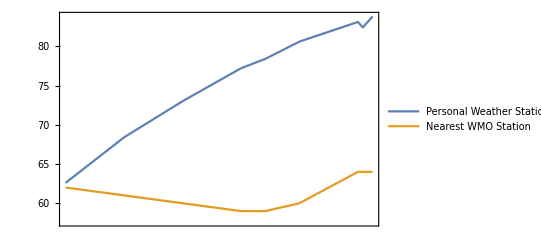

```mathematica
(*Collect all the Blockchain sumbissions from the weather station and chart the temperature over time*)  
Databin["EM6FHeXi", All];
recentHashes=Normal[Dataset[Databin["EM6FHeXi", -10]]][[All,1,-1]];
data=Dataset[BlockchainGet[recentHashes]];
times=data[[1;;All,2,2]]//Normal;
temps=data[[1;;All,2,1,1,2]]//Normal;
myTempsTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@temps}]];
wmoTempsTimeSeries=TimeSeries[Transpose[{times, AirTemperatureData["KBED", times]}]];
DateListPlot[{myTempsTimeSeries,wmoTempsTimeSeries}, PlotLegends->{"Personal Weather Station","Nearest WMO Station"}]
```

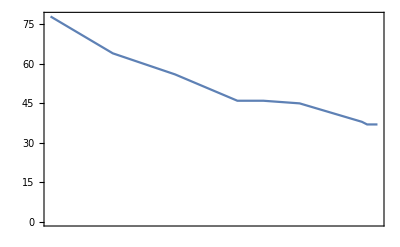

TimeSeries[…]

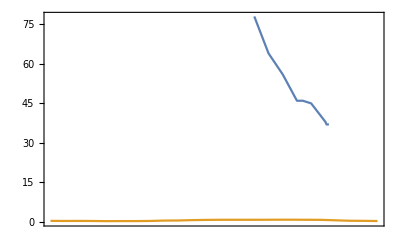

```mathematica
(*Chart the weather station's Humidity*)
humidity=data[[1;;All,2,1,2,2]]//Normal;
DateListPlot[Transpose[{times, MapAt[ToExpression,#,1]&/@humidity}]]

myHumidityTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@humidity}]];
wmoHumidityTimeSeries=WeatherData["KBED","Humidity",{Now-Quantity[1, "Days"], Now}]
DateListPlot[{myHumidityTimeSeries,wmoHumidityTimeSeries}]
```

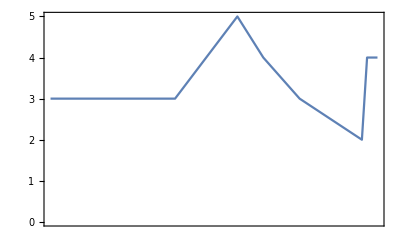

4.7 mi/h

```mathematica
(*Chart the weather station's Wind Speed*)
windSpeed=data[[1;;All,2,1,3,2]]//Normal;
DateListPlot[Transpose[{times, MapAt[ToExpression,#,1]&/@windSpeed}]]
WindSpeedData["KBED", Now]
```

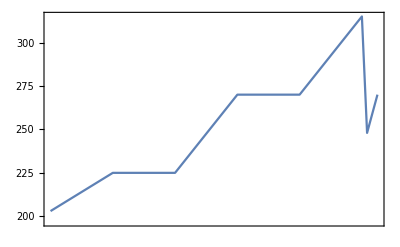

340. °

```mathematica
(*Chart the weather station's Wind Direction*)
windDirection=data[[1;;All,2,1,4,2]]//Normal;
DateListPlot[Transpose[{times, MapAt[ToExpression,#,1]&/@windDirection}]]
WindDirectionData["KBED", Now]
```

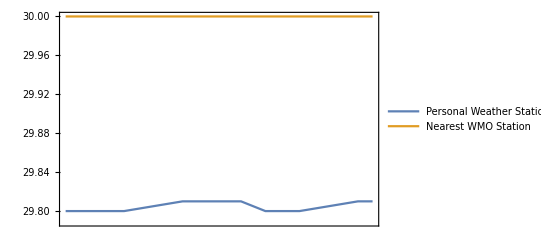

```mathematica
(*Chart the weather station's Pressure*)
pressure=data[[1;;All,2,1,7,2]]//Normal;

myPressureTimeSeries=TimeSeries[Transpose[{times, MapAt[ToExpression,#,1]&/@pressure}]];
wmoPressureTimeSeries=TimeSeries[Transpose[{times, AirPressureData["KBED", times]}]];
DateListPlot[{myPressureTimeSeries,wmoPressureTimeSeries}, PlotLegends->{"Personal Weather Station","Nearest WMO Station"}]
```